# FP Convergence Analysis

## Preliminaries

```mathematica
maindir=SetDirectory[NotebookDirectory[]]
nbf=NotebookFileName[]
```

/storage/disqs/CCxD/Analysis_SS

/storage/disqs/CCxD/Analysis_SS/FPConvergeAnalysis_SS-BS.nb

### Setting Parameters

```mathematica
matrix = 0;
configs = 500000000;
iditer = 3;
zrange = 25;
cropamt = 8;
bootstrapsets = 10;
bootstrapamt = 1;
gdamt = 0;
project="CCGD";
importrange = Table[i,{i,1,(rgsteps = 15)}];
```

## Importing Data

```mathematica
datadir=maindir<>"/../"<>project<>"/data/";
SetDirectory[datadir];
filepath = datadir<>ToString[matrix]<>"-RG-"<>ToString[configs]<>"-"<>ToString[iditer]<>"-"<>ToString[gdamt]<>"/dists/BS";
zimport = Table[Flatten[Import[ToString[filepath]<>ToString[i]<>"/"<>ToString[j]<>"/"<>ToString[matrix]<>"-z"<>"-"<>ToString[configs]<>"-averaged"<>".txt","Data"]],{i,1,bootstrapamt},{j,importrange}];
timport = Table[Flatten[Import[ToString[filepath]<>ToString[i]<>"/"<>ToString[j]<>"/"<>ToString[matrix]<>"-t"<>"-"<>ToString[configs]<>"-averaged"<>".txt","Data"]],{i,1,bootstrapamt},{j,importrange}];
gimport = Table[Flatten[Import[ToString[filepath]<>ToString[i]<>"/"<>ToString[j]<>"/"<>ToString[matrix]<>"-g"<>"-"<>ToString[configs]<>"-averaged"<>".txt","Data"]],{i,1,bootstrapamt},{j,importrange}];
croppedzimport = Table[Take[Flatten[Import[ToString[filepath]<>ToString[i]<>"/"<>ToString[j]<>"/"<>ToString[matrix]<>"-z"<>"-"<>ToString[configs]<>"-averaged"<>".txt","Data"]],{1000* (zrange -cropamt),1000*(zrange+cropamt)}],{i,1,bootstrapamt},{j,importrange}];
```

## Normalizing and Plotting Data

```mathematica
ttotal = Table[Total[ToExpression[Take[timport[[i]][[j]],{2,999}]]],{i,1,bootstrapamt},{j,1,Length[importrange]}];
gtotal = Table[Total[ToExpression[Take[gimport[[i]][[j]],{2,999}]]],{i,1,bootstrapamt},{j,1,Length[importrange]}];
ztotal = Table[Total[zimport[[i]][[j]]],{i,1,bootstrapamt},{j,1,Length[importrange]}];
tnormalized = Table[{k/1000,1000*ToExpression[timport[[i]][[j]][[k]]]/ttotal[[i]][[j]]},{i,1,bootstrapamt},{j,1,Length[importrange]},{k,2,Length[timport[[1]][[1]]]-1}];
gnormalized = Table[{k/1000,1000*ToExpression[gimport[[i]][[j]][[k]]]/gtotal[[i]][[j]]},{i,1,bootstrapamt},{j,1,Length[importrange]},{k,2,Length[gimport[[1]][[1]]-1]}];
znormalized = Table[{(k/1000)-(zrange + 0.0005),1000*zimport[[i]][[j]][[k]]/ztotal[[i]][[j]]},{i,1,bootstrapamt},{j,1,Length[importrange]},{k,1,Length[zimport[[1]][[1]]]}];
zcroppednormalized = Table[Take[znormalized[[i]][[j]],{1000* (zrange -cropamt),1000*(zrange+cropamt)}],{i,1,bootstrapamt},{j,1,Length[importrange]}];
```

```mathematica
ttrans = Transpose[tnormalized,1<->4];
gtrans = Transpose[gnormalized,1<->4];
ztrans = Transpose[znormalized,1<->4];
```

```mathematica
tavg = Table[{tnormalized[[1]][[1]][[j]][[1]],Total[ttrans[[2]][[i]][[j]]]},{i,1,Length[importrange]},{j,1,Length[tnormalized[[1]][[1]]]}];
gavg = Table[{gnormalized[[1]][[1]][[j]][[1]],Total[gtrans[[2]][[i]][[j]]]},{i,1,Length[importrange]},{j,1,Length[gnormalized[[1]][[1]]]}];
zavg = Table[{znormalized[[1]][[1]][[j]][[1]],Total[ztrans[[2]][[i]][[j]]]},{i,1,Length[importrange]},{j,1,Length[znormalized[[1]][[1]]]}];
zcroppedavg = Table[Take[zavg[[i]],{1000* (zrange -cropamt),1000*(zrange+cropamt)}],{i,1,Length[importrange]}];
```

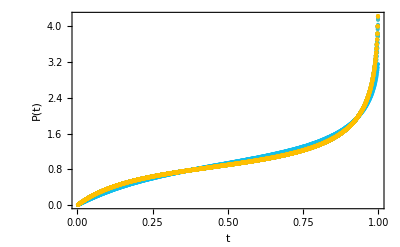

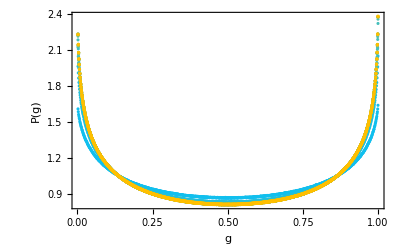

-Graphics-

-Graphics-

Part::partw: Part 2 of {{{{-24.9995, 0.}, {-24.9985, 0.}, {-24.9975, 0.}, {-24.9965, 0.}, {-24.9955, 0.}, {-24.9945, 0.}, {-24.9935, 0.}, <<49989>>, {<<7>>, 0.}, {24.9975, 0.}, {24.9985, 0.}, {24.9995, 0.}}, <<14>>}} does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: {{{{-24.9995, 0.}, {-24.9985, 0.}, {-24.9975, 0.}, {-24.9965, 0.}, {-24.9955, 0.}, {-24.9945, 0.}, {-24.9935, 0.}, <<49990>>, {24.9975, 0.}, {24.9985, 0.}, {24.9995, 0.}}, <<14>>}}[[2]] is not a list of numbers or pairs of numbers.

ListPlot[{{1}}⟦2⟧]
 |  |  |  |

Part::partw: Part 2 of {{{{1/500,0.00489184},{3/1000,0.00836508},{1/250,0.0116718},{1/200,0.01483},{3/500,0.0182471},{7/1000,0.0215698},{1/125,0.0250531},{9/1000,0.0281652},{1/100,0.0314257},{11/1000,0.0350073},«988»},{{1/500,0.00660639},{3/1000,0.0106586},{1/250,0.0151204},{1/200,0.0191224},{3/500,0.0233232},{7/1000,0.0273533},{1/125,0.0316062},{9/1000,0.0357548},{1/100,0.039803},{11/1000,0.044321},«988»},«8»,«5»}} does not exist.

Part::partw: Part 2 of {{{{0.002,0.00489184},{0.003,0.00836508},{0.004,0.0116718},{0.005,0.01483},{0.006,0.0182471},{0.007,0.0215698},{0.008,0.0250531},{0.009,0.0281652},{0.01,0.0314257},{0.011,0.0350073},«988»},{{0.002,0.00660639},{0.003,0.0106586},{0.004,0.0151204},{0.005,0.0191224},{0.006,0.0233232},{0.007,0.0273533},{0.008,0.0316062},{0.009,0.0357548},{0.01,0.039803},{0.011,0.044321},«988»},«8»,«5»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: {{{{0.002,0.00489184},{0.003,0.00836508},{0.004,0.0116718},{0.005,0.01483},{0.006,0.0182471},{0.007,0.0215698},{0.008,0.0250531},{0.009,0.0281652},{0.01,0.0314257},{0.011,0.0350073},«988»},{{0.002,0.00660639},{0.003,0.0106586},{0.004,0.0151204},{0.005,0.0191224},{0.006,0.0233232},{0.007,0.0273533},{0.008,0.0316062},{0.009,0.0357548},{0.01,0.039803},{0.011,0.044321},«988»},«8»,«5»}}⟦2⟧ is not a list of numbers or pairs of numbers.

ListPlot[{{{{1/500,0.00489184},{3/1000,0.00836508},{1/250,0.0116718},{1/200,0.01483},{3/500,0.0182471},{7/1000,0.0215698},{1/125,0.0250531},{9/1000,0.0281652},{1/100,0.0314257},{11/1000,0.0350073},{3/250,0.0376439},{13/1000,0.0416649},{7/500,0.0453669},973,{247/250,2.68994},{989/1000,2.71373},{99/100,2.74447},{991/1000,2.7769},{124/125,2.80911},{993/1000,2.84564},{497/500,2.87939},{199/200,2.92055},{249/250,2.96886},{997/1000,3.01874},{499/500,3.07404},{999/1000,3.14945}},13,{1}}}⟦2⟧]
 |  |  |  |

```mathematica
tplot=List[];
gplot = List[];
zplot = List[];
croppedzplot = List[];
For[i=1,i<=Length[importrange],i++,
(
AppendTo[tplot,ListPlot[tavg[[i]],PlotStyle->RGBColor[i/Length[importrange],0.75,1-(i/Length[importrange])]]];
AppendTo[gplot,ListPlot[gavg[[i]],PlotStyle->RGBColor[i/Length[importrange],0.75,1-(i/Length[importrange])]]];
AppendTo[zplot,ListPlot[zavg[[i]],PlotStyle->RGBColor[i/Length[importrange],0.75,1-(i/Length[importrange])]]];
AppendTo[croppedzplot,ListPlot[zcroppedavg[[i]],PlotStyle->RGBColor[i/Length[importrange],0.75,1-(i/(Length[importrange]))]]];
)];
Show[tplot, Frame->True,PlotRange->{{0,1},{0,Automatic}},LabelStyle->{FontSize->24}, FrameLabel->{t,"P(t)"}]
Show[gplot,Frame->True, PlotRange->{{0,1},{0,Automatic}},LabelStyle->{FontSize->24},FrameLabel->{g,"P(g)"}]
Show[zplot,Frame->True,PlotRange->All,LabelStyle->{FontSize->24},FrameLabel->{z,"Q(z)"}]
Show[croppedzplot,Frame->True,PlotRange->{Automatic,{0,Automatic}},LabelStyle->{FontSize->24},FrameLabel->{z,"Q(z)"}]
ListPlot[znormalized[[2]]]
ListPlot[tnormalized[[2]]]
```

## Analysis

```mathematica
ex = Table[zavg[[i]][[j]][[1]]*zavg[[i]][[j]][[2]]*(1/1000),{i,1,Length[importrange]},{j,1,Length[zavg[[1]]]}];
exsquared = Table[zavg[[i]][[j]][[1]]^2*zavg[[i]][[j]][[2]]*(1/1000),{i,1,Length[importrange]},{j,1,Length[zavg[[1]]]}];
var = Table[Total[exsquared[[i]]]-Total[ex[[i]]]^2,{i,1,Length[importrange]}];
stdev = Table[Sqrt[var[[i]]],{i,1,Length[importrange]}];
difference = Table[Abs[zavg[[i+1]][[j]][[2]]-zavg[[i]][[j]][[2]]]^2,{i,1,Length[zavg]-1},{j,1,Length[zavg[[1]]]}];
delta = Table[Sqrt[(1/1000)*(Total[difference[[i]]])],{i,1,Length[zavg]-1}];
```

#### Variance as a function of RG step

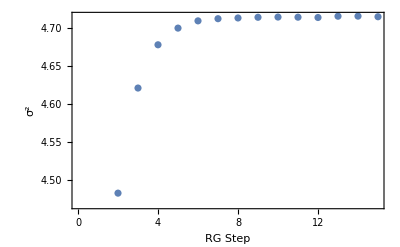

{4.13502,4.48268,4.62105,4.678,4.69995,4.70949,4.71236,4.7133,4.7142,4.7145,4.71433,4.71393,4.71562,4.71573,4.71494}

```mathematica
ListPlot[var, Frame->True, LabelStyle->{FontSize->24},FrameLabel->{"RG Step",σ^2}]
var
```

#### Standard Deviation as a function of RG step

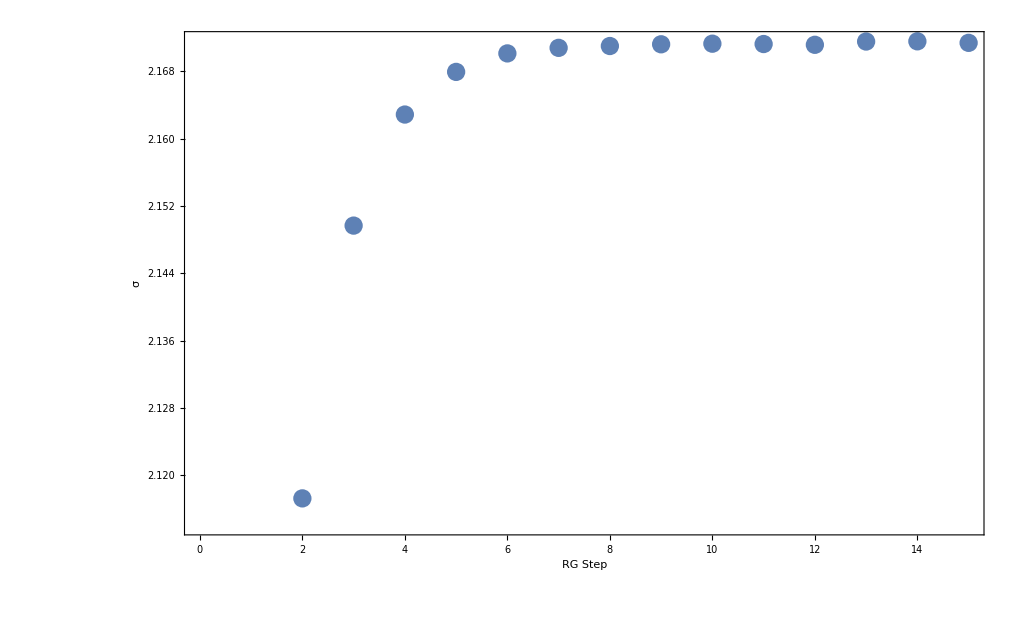

{2.03347,2.11723,2.14966,2.16287,2.16794,2.17014,2.1708,2.17101,2.17122,2.17129,2.17125,2.17116,2.17155,2.17157,2.17139}

```mathematica
ListPlot[stdev, Frame->True, LabelStyle->{FontSize->24},FrameLabel->{"RG Step","σ"}]
stdev
```

#### Difference between successive RG steps as a function of RG step

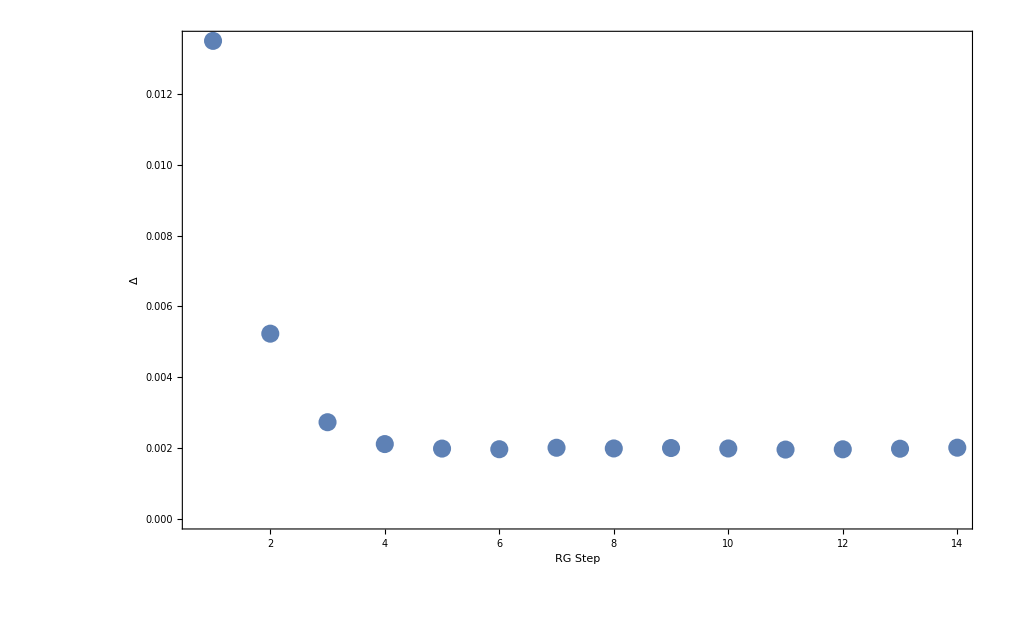

```mathematica
ListPlot[delta,Frame->True, LabelStyle->{FontSize->24},FrameLabel->{"RG Step","Δ"}, PlotRange->Full]
```

```mathematica
delta
```

{0.0134846,0.00523374,0.00273854,0.00212263,0.00199551,0.00197744,0.00201892,0.00199904,0.00201138,0.00199843,0.00196755,0.00197522,0.0019916,0.00202078}

## Saving

```mathematica
Directory[]
SetDirectory[maindir]
```

/storage/disqs/CCxD/CCGD/data

/storage/disqs/CCxD/Analysis_SS

```mathematica
nbf=NotebookFileName[]
NotebookSave[EvaluationNotebook[],"FPAnalysis-"<>ToString[project]<>"-"<>ToString[configs]<>"-"<>ToString[matrix]<>"-"<>DateString[{"Day","-","Month","-","Year"}]<>".nb"]
NotebookSave[EvaluationNotebook[],nbf]
```

/storage/disqs/CCxD/Analysis_SS/FPConvergeAnalysis_SS-BS.nb